```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;m=1;a=1;V[r_]=-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r];VCou[r_]=-α/r;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2[r_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086};
```

```mathematica
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefV[r].mx
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefVs2[r].mx
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Integration1st=NIntegrate[efVs2[[#]]/r δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
Integration2nd=NIntegrate[efVs2[[#]]/r Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

{-0.0419061549670537030936150727826,0.000817405135691683610681411802699,0.00053890199500076025275734509527,-0.000354634840965060883574431934863,-0.000252703599986847964346093565526,0.000191005384409732759367603433539,-0.000150650494273192937723585477227,0.000122649667028868463994494150484,0.000102319018502448651747455269067,-0.0000870216778373596614694729326333,-0.0000751769880497682285712555995699,0.0000657877472090331060928652485178,0.0000581977778106023655331939969117,-0.0000519598224019271305249819385656,-0.0000467597955011401678772626125872,-0.0000423714176590134319226863564397,0.0000386280179114495315830726549105,0.0000354044305875534502796493522592,-0.0000326050410225466066294554320115,0.0000301557946924895191232442424903}

{0.0677424829055347463085675876383,0.0266444264849977915794943071336,0.0117927087492052688936431701069,-0.00708081517484211498614106898637,-0.0048640050689080877191308923772,0.00360920832583376961598509188255,-0.00281658864876770514079855907354,0.00227781268972087515015123926164,0.0018917503377637070522425636555,-0.00160386592792814412132174755917,-0.00138238116050496081321335984321,0.0012076393602717717348631730473,0.0010668900654766965983924274602,-0.000951535399184031482928960463928,-0.000855587364630334087225105528652,-0.000774760051040688117623608258417,0.000705913071439274966673405068832,0.000646698118824392936303082650082,-0.00059532762122045500754729414781,0.000550421315091884486640711645395}

```mathematica
ψrTrue[n_,r0_][Z_,γ_,η_]:=Z NLimit[efVs2[[n]]/(√(4π)r),r->r0]+√(4π)(γ Integration1st[[n]]+η a^2 Integration2nd[[n]])
```

```mathematica
ψrTrue[1,0][1,1,1]
```

```mathematica
NumberQ@Zl
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={18,19,20},Zstart=1,γstart=1,ηstart=1},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;
PrintTemporary[REAL];*)
REF=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@REFRANGE;
(*PrintTemporary[REF];*)
RES=FindRoot[Thread[ψrTrue[#,r0][Z,γ,η]&/@REFRANGE==REF],{{Z,Zstart},{γ,γstart},{η,ηstart}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30(*,StepMonitor:>Print[{Z,γ,η}]*)];
(*ψr=ψrTrue[#,r0][Z,γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];
Print[{Z,{r0,γ},{r0,η}}/.RES];*)
{Zstart,γstart,ηstart}={Z,γ,η}/.RES;
(*Print[{Zstart,γstart,ηstart}];*)
{{r0,Z},{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0]
```

FindRoot::precw: The precision of the argument function ({-0.00543717 Z+2 √π (0.0000354044305875534502796493522592 γ+0.000646698118824392936303082650082 η)==-0.0108501,0.00500595 Z+2 √π (-0.0000326050410225466066294554320115 γ-0.00059532762122045500754729414781 η)==0.00998964,-0.00462897 Z+2 √π (0.0000301557946924895191232442424903 γ+0.000550421315091884486640711645395 η)==-0.00923711}) is less than WorkingPrecision (30.).

{{0,-1.11607033397923234010176824984},{0,-47.1550698036605712314901485102},{0,-4.79835298186353787906520142013}}

```mathematica
Zl={};γl={};ηl={};
```

```mathematica
Quiet@Module[{max,h},Zl={};γl={};ηl={};Monitor[Table[Module[{γη},
γη=Determine[r0];
AppendTo[Zl,γη[[1]]];
AppendTo[γl,γη[[2]]];
AppendTo[ηl,γη[[3]]];]
,{r0,0,1,0.0005}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Transpose@Partition[N[Zl,6],10]//TableForm
Transpose@Partition[N[Zl,6],10]//TableForm
Transpose@Partition[N[Zl,6],10]//TableForm
```

```mathematica
Zr=Interpolation[Zl]
γr=Interpolation[γl]
ηr=Interpolation[ηl]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

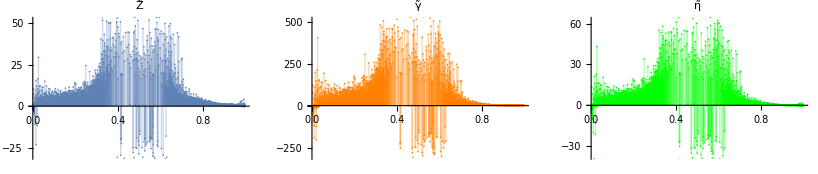

C:\Users\ASUS\OneDrive\Documents\Test_6\psirmodified2_2.eps

```mathematica
GraphicsGrid@{{ListPlot[Zl,Filling->Axis,ImageSize->250,PlotLabel->Style["Z̃",15],FrameTicksStyle->15],ListPlot[γl,Filling->Axis,ImageSize->250,PlotStyle->Orange,PlotLabel->Style["γ̃",15],FrameTicksStyle->Directive[Bold,11]],ListPlot[ηl,Filling->Axis,ImageSize->250,PlotStyle->Green,PlotLabel->Style["η̃",15]]}}
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\psirmodified2_2.eps",%]
```

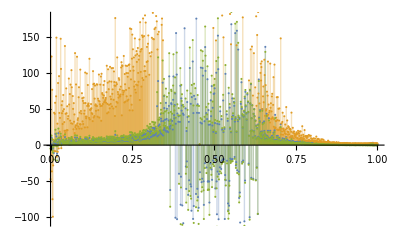

```mathematica
ListPlot[{Zl,γl,ηl},Filling->Axis]
```

```mathematica
ψrfun[r_][n_]:=Zr[r] efVs2[[n]]/(√(4π)r)+√(4π)(γr[r] Integration1st[[n]]+ηr[r] a^2 Integration2nd[[n]])
```

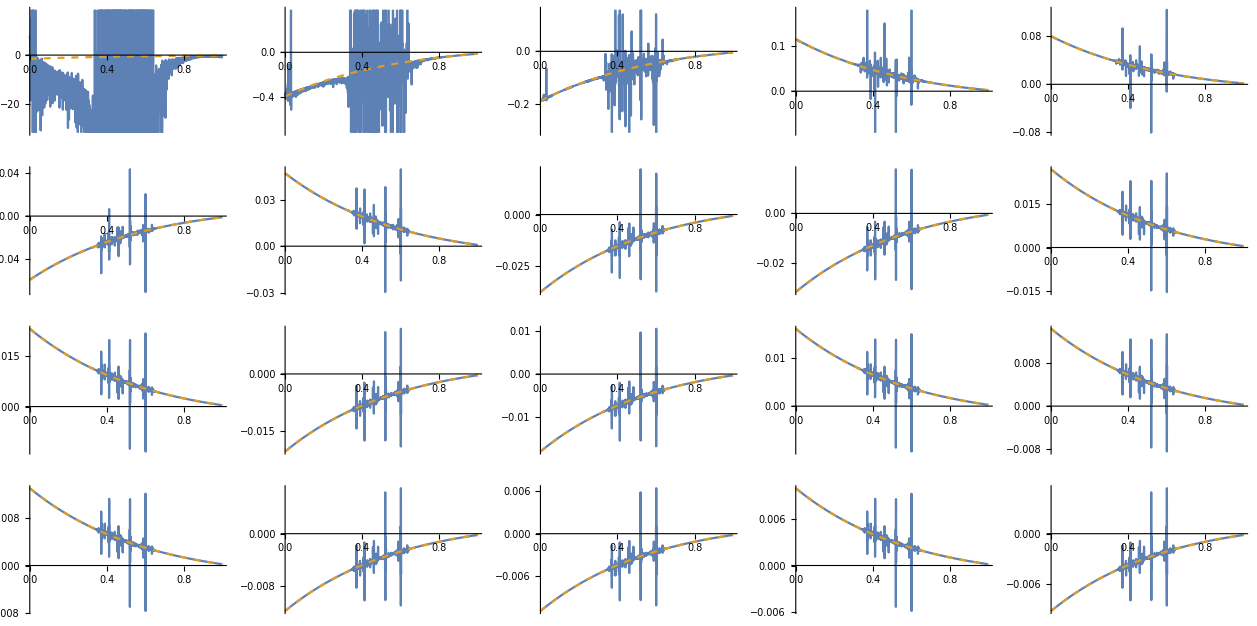

C:\Users\ASUS\OneDrive\Documents\Test_6\psirmodified2.eps

```mathematica
GraphicsGrid@Partition[Table[Plot[{ψrfun[r][n],efV[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\psirmodified2.eps",%]
```